/home/gwang/Code/AktMuscleCode/NOB_DB_Gsu10_iVol0p075/

{6.144,6.144,6.144,6.144,6.14401,6.14401,6.14402,6.14403,6.14404,6.14405,6.14406,6.14407,6.14409,6.1441,6.14412,6.14414,6.14415,6.14418,6.1442,6.14422,6.14425,6.14427,6.1443,6.14433,6.14436,6.14439,6.14442,6.14445,6.14449,6.14452,6.14456,6.1446,6.14464,6.14468,6.14472,6.14477,6.14481,6.14486,6.14491,29923,5.21942,5.21943,5.21943,5.21944,5.21944,5.21945,5.21945,5.21946,5.21947,5.21947,5.21948,5.21948,5.21949,5.21949,5.2195,5.2195,5.2195,5.21951,5.21951,5.21952,5.21952,5.21953,5.21953,5.21954,5.21954,5.21954,5.21955,5.21955,5.21955,5.21956,5.21956,5.21957,5.21957,5.21957,5.21958,5.21958,5.21958,5.21959,5.21959}
 |  |  |  |

4.50695

1.51429

0.417536

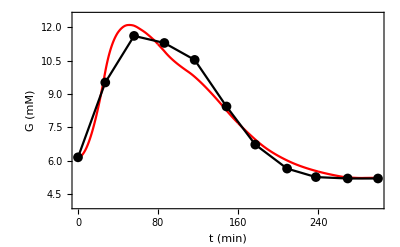

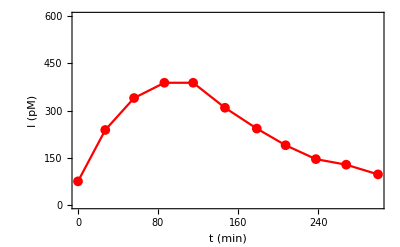

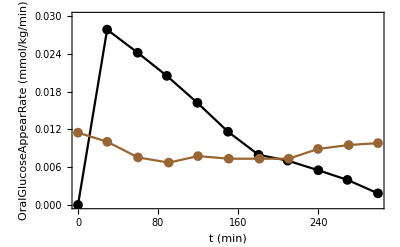

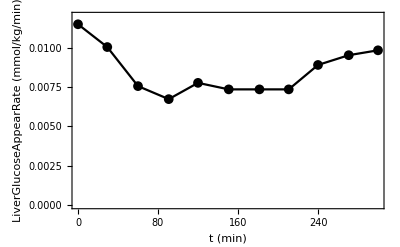

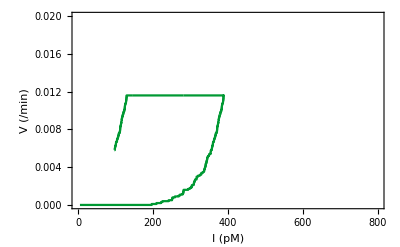

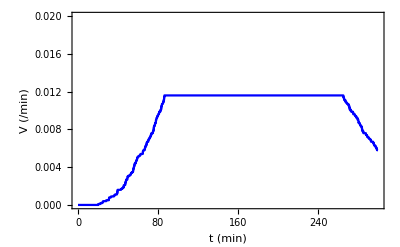

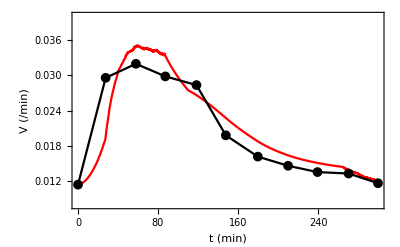

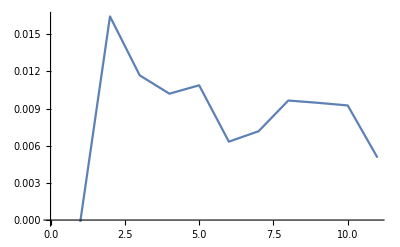

```mathematica
Remove["Global`*"];

NotebookDirectory[]

h=0.01;

OralData=Flatten[Import[ToFileName[NotebookDirectory[],"iOral.txt"],"Data"]];
LiverData=Flatten[Import[ToFileName[NotebookDirectory[],"iLiver.txt"],"Data"]];
OraliverData=Flatten[Import[ToFileName[NotebookDirectory[],"iMeal.txt"],"Data"]];
s0=OraliverData[[1]];

BestParaBlock=Flatten[Import[ToFileName[NotebookDirectory[],"BestParaBlock.txt"],"Data"]];
Vsu=BestParaBlock[[4]];
Gsu=BestParaBlock[[5]];
Ome=BestParaBlock[[6]];


G=Flatten[Import[ToFileName[NotebookDirectory[],"G.txt"],"Data"]]
Len = Length[G];
Insulin=Flatten[Import[ToFileName[NotebookDirectory[],"I.txt"],"Data"]];

V=Flatten[Import[ToFileName[NotebookDirectory[],"V.txt"],"Data"]];


VofI = MapThread[List,{Insulin,V}];

V0=s0/Ome/G[[1]];

GGsu = G-Gsu;
GGsu = GGsu /. _?Negative -> 0;

VGO= (V+V0) G Ome + Vsu GGsu Ome;

VG = V G;

TotalV0 = (Total[G]-0.5 G[[1]]-0.5 G[[Len]]) V0 Ome h

TotalVI=(Total[VG]-0.5 VG[[1]]-0.5 VG[[Len]])  Ome h

TotalVsu=Total[GGsu] Vsu Ome h

VGOData=Flatten[Import[ToFileName[NotebookDirectory[],"VGOData.txt"],"Data"]];
VGOTime=Flatten[Import[ToFileName[NotebookDirectory[],"VGOTime.txt"],"Data"]];
VGODataTime = MapThread[List,{VGOTime,VGOData}];




GData=Flatten[Import[ToFileName[NotebookDirectory[],"GData.txt"],"Data"]];
IData=Flatten[Import[ToFileName[NotebookDirectory[],"IData.txt"],"Data"]];
GTime=Flatten[Import[ToFileName[NotebookDirectory[],"GTime.txt"],"Data"]];
ITime=Flatten[Import[ToFileName[NotebookDirectory[],"ITime.txt"],"Data"]];
OralTime=Flatten[Import[ToFileName[NotebookDirectory[],"iOralTime.txt"],"Data"]];
LiverTime=Flatten[Import[ToFileName[NotebookDirectory[],"iLiverTime.txt"],"Data"]];
LenTime=Length[GTime];
GDataTime = MapThread[List,{GTime,GData}];
IDataTime = MapThread[List,{ITime,IData}];
OralDataTime=MapThread[List,{OralTime,OralData}];
LiverDataTime=MapThread[List,{LiverTime,LiverData}];




Show[
ListLinePlot[G,DataRange->{0,Len*h},PlotRange->{{0,300},{4,12.5}},Frame->True,FrameLabel->{"t (min)","G (mM)"},LabelStyle->20,FrameTicksStyle->Directive[18],PlotStyle->Red],
ListLinePlot[GDataTime,PlotMarkers->{Automatic, 10},PlotStyle->Black]
]

Export[ToFileName[NotebookDirectory[],"GData.eps"],%];

(*
Show[
ListLinePlot[Insulin,DataRange->{0,Len*h},PlotRange->{{0,300},{0,600}},Frame->True,FrameLabel->{"t (min)","I (pM)"},LabelStyle->20,FrameTicksStyle->Directive[18],PlotStyle->Red],
ListPlot[IDataTime,PlotMarkers->{Automatic, 10},PlotStyle->Red]
]
*)

ListLinePlot[IDataTime,PlotMarkers->{Automatic, 10},PlotStyle->Red,PlotRange->{{0,300},{0,600}},Frame->True,FrameLabel->{"t (min)","I (pM)"},LabelStyle->20,FrameTicksStyle->Directive[18]]

Export[ToFileName[NotebookDirectory[],"IData.eps"],%];

Show[
ListLinePlot[OralDataTime,PlotMarkers->{Automatic,10},PlotStyle->Black,PlotRange->{{0,300},{0,0.030}},Frame->True,FrameLabel->{"t (min)","OralGlucoseAppearRate (mmol/kg/min)"},LabelStyle->15,FrameTicksStyle->Directive[14]],
ListLinePlot[LiverDataTime,PlotMarkers->{Automatic,10},PlotStyle->Brown]
]
Export[ToFileName[NotebookDirectory[],"Oral.eps"],%];


ListLinePlot[LiverDataTime,PlotMarkers->{Automatic,10},PlotStyle->Black,PlotRange->{{0,300},{0,0.012}},Frame->True,FrameLabel->{"t (min)","LiverGlucoseAppearRate (mmol/kg/min)"},LabelStyle->15,FrameTicksStyle->Directive[18]]

Export[ToFileName[NotebookDirectory[],"Liver.eps"],%];

ListLinePlot[VofI,PlotRange->{{0,800},{0,0.02}},Frame->True,FrameLabel->{"I (pM)","V (/min)"},LabelStyle->20,FrameTicksStyle->Directive[18],PlotStyle->RGBColor[0,0.6,0.2]]


Export[ToFileName[NotebookDirectory[],"VI.eps"],%];

ListLinePlot[V,DataRange->{0,Len*h},PlotRange->{{0,300},{0,0.02}},Frame->True,FrameLabel->{"t (min)","V (/min)"},LabelStyle->20,FrameTicksStyle->Directive[18],PlotStyle->Blue]

Show[
ListLinePlot[VGO,DataRange->{0,Len*h},PlotRange->{{0,300},{0.008,0.04}},Frame->True,FrameLabel->{"t (min)","V (/min)"},LabelStyle->20,FrameTicksStyle->Directive[18],PlotStyle->Red],
ListLinePlot[VGODataTime,PlotMarkers->{Automatic, 10},PlotStyle->Black]
]

Export[ToFileName[NotebookDirectory[],"VGO.eps"],%];

ListLinePlot[VGOData/GData/0.075-ConstantArray[V0,Length[VGOData]]]
```